## simple example, 2 gnd states coupled to single excited state/

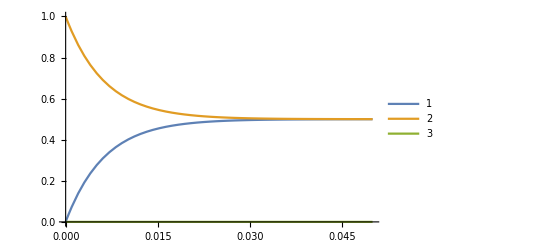

```mathematica
Clear["Global`*"]
MHz = 10^6;
kHz=10^3;
Ω=.1MHz;
Γ= 2π 5 MHz;
us = 10^-6;
ms=10^-3;

Ω13=Ω;
Ω23=Ω;
Γ31=Γ;
Γ32=Γ;


Γ3=(Γ31+Γ32);

v1=Transpose@{Subscript[P, #]'[t]&/@Range[3]};
v2=Transpose@{Subscript[P, #][t]&/@Range[3]};

m={
{-Ω13^2/Γ3,0,Ω13^2/Γ3+Γ31},
{0,-Ω23^2/Γ3,Ω23^2/Γ3+Γ32},
{Ω13^2/Γ3,Ω23^2/Γ3,-Ω13^2/Γ3-Ω23^2/Γ3-Γ3}
};

soln=DSolve[{
v1[[1,1]]==(m.v2)[[1,1]],
v1[[2,1]]==(m.v2)[[2,1]],
v1[[3,1]]==(m.v2)[[3,1]],

v2[[1,1]]==0/.t->0,
v2[[2,1]]==1/.t->0,
v2[[3,1]]==0/.t->0

},Subscript[P, #]&/@Range[3],t];
Plot[{Subscript[P, 1][t]/.soln[[1]],Subscript[P, 2][t]/.soln[[1]],Subscript[P, 3][t]/.soln[[1]]},{t,0,50ms},PlotLegends->Automatic]
```

## multilevel Cs Single excited state F4. Ground states F3, F4 diagonal decay should all be -ve!!

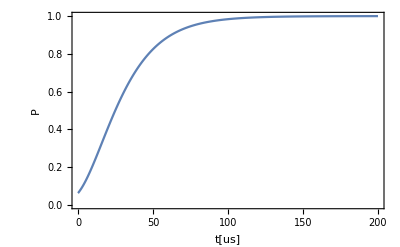

```mathematica
Clear["Global`*"]

MHz = 10^6;
kHz=10^3;
us = 10^-6;
ms=10^-3;

JJ=1;4.4786;

Fe=4;
Fg1=4;
Fg2=3;

{ΩF4,ΩF3}={7,20}MHz;{20,20}MHz; (*these units come with some prefactor--dn't take too seriously...*)
Γ= 2π 5. MHz;

(*which gnd state to monitor*)
{F,mF}={4,4};{4,0};

(*intensities in each polarization of incident drive radiation*)
POL= {0,0,1};{0,1,0};(*sigma-,pi,sigma+*)

(*simulation params*)
Δt=1./Γ;2.6/Γ;
tEnd=200us;200us;

(*Fg,σp,π0,σm,Ω,POL*)
(*list params in order of DECREASING F!!! (for later definition of iMon)*)
params1=
{Fg1, 
JJ{7/120,49/480,21/160,7/48,7/48,21/160,49/480,7/120},
JJ{-7/30,-21/160,-7/120,-7/480,0,7/480,7/120,21/160,7/30},
-JJ{7/120,49/480,21/160,7/48,7/48,21/160,49/480,7/120},
ΩF4,
POL
};

params2=
{Fg2, 
 JJ{7/72,7/96,5/96,5/144,1/48,1/96,1/288},
JJ{7/288,1/24,5/96,1/18,5/96,1/24,7/288},
Reverse[ JJ{7/72,7/96,5/96,5/144,1/48,1/96,1/288}],
ΩF3,
POL
};

(*Functions to Pad with Zero rows or columns either at first or last position.*)
AddRows[list0_,pos0_,n0_]:=
Module[{list=list0,pos = pos0,n=n0},
(*pos=-1, add to end, anything else-->add to beginning*)
If[pos==-1,
list=Join[list,ConstantArray[0,{n,Length[list]}]],
list=Join[ConstantArray[0,{n,Length[list]}],list]
]
];

AddColumns[list0_,pos0_,n0_]:=
Module[{list=list0,pos = pos0,n=n0},
(*pos=-1, add to end, anything else-->add to beginning*)
If[pos==-1,
list=PadRight[#,Length[#]+n]&/@list,
list=PadLeft[#,Length[#]+n]&/@list
]
];

GenerateDecay[Fe0_,Fg0_,σp0_,π00_,σm0_]:=
Block[{Fe=Fe0,Fg=Fg0,σp=σp0,π0=π00,σm=σm0},

Mπ0=DiagonalMatrix[π0];
Mσm=DiagonalMatrix[σm];
Mσp=DiagonalMatrix[σp];


Switch[Fe-Fg ,
-1,
Mσp=AddRows[Mσp,-1,2];
Mπ0=AddRows[Mπ0,-1,1];
Mπ0=AddRows[Mπ0,1,1];
Mσm=AddRows[Mσm,1,2];,

0,
Mσp=AddRows[Mσp,-1,1];
Mσp=AddColumns[Mσp,1,1];
Mσm=AddRows[Mσm,1,1];
Mσm=AddColumns[Mσm,-1,1];,

1,
Mσp=AddColumns[Mσp,1,2];
Mπ0=AddColumns[Mπ0,-1,1];
Mπ0=AddColumns[Mπ0,1,1];
Mσm=AddColumns[Mσm,-1,2];

];

(*generate block matrix for decays from E-->G*)
Mσp+Mπ0+Mσm
];

(*--------------------------------------------------generate decay matrix-----------------------------------------------------------*)
b=Reap[Do[
{Fg,σp,π0,σm,Ω,POL}=params;
(*generate block matrix for ALL decays out of E-->G*)
Sow[{Fg,GenerateDecay[Fe,Fg,σp,π0,σm]}];
,{params,{params1,params2}}]
][[2,1]];

(*sort from largest Fg to smallest Fg*)
b=Sort[b,#1[[1]]>#2[[1]]&];
(*concatenate Gnd state matrices together, vertically.*)
b=Join[Flatten[b[[;;,2]],1]];
(*-use ABS, all +ve, because decays go INTO gnd state, not out of it.*)
b=Abs[b]; 

(*normalize columns to Γ*)
b=Γ Transpose[ #/Total[#]&/@Transpose[b]];
a=-DiagonalMatrix[Total[#]&/@Transpose[b]];(*more general; check that all entries add up to Γ*)
(*create full matrix for decay from Fe to Fg*)
c=Join[a,b];
MΓ=AddColumns[c,-1,Abs[Length[c]-Length[c[[1]]]]];

(*-----------------------------------------------------------generate drive matrix-----------------------------------------------------------*)
b=Reap[Do[
{Fg,σp,π0,σm,Ω,POL}=params;
pol=Ω^2/Γ POL;(*sigma-, pi, sigma+*)
(*assuming there is only 1 excited state with decay Γ*)
{σm,π0,σp}=pol{σm,π0,σp};
(*generate block matrix for ALL decays out of E-->G*)
Sow[{Fg,GenerateDecay[Fe,Fg,σp,π0,σm]}];
,{params,{params1,params2}}]][[2,1]];

(*sort from largest Fg to smallest Fg*)
b=Sort[b,#1[[1]]>#2[[1]]&];
(*concatenate G matrices together, vertically.*)
b=Join[Flatten[b[[;;,2]],1]];
(*-use ABS, all +ve, because decays go INTO gnd state, not out of it.*)
b=Abs[b]; 

a=-DiagonalMatrix[Total[#]&/@Transpose[b]];(*perform vertical sum to get total coupling to excited state*)
d=-DiagonalMatrix[Total[#]&/@b];(*perform horiz sum to get total coupling from ground state*)

(*-----------------------------------------------------------combine all block matrices-----------------------------------------------------------*)
c=Join[a,b];
c=AddColumns[c,-1,Abs[Length[c]-Length[c[[1]]]]];
(*join vertically*)
e=Join[a,b];
f=Join[Transpose[b],d];
MΩ=Join[e,f,2]; (*join horizontally*)
MH=MΩ+MΓ;

(*-----------------------------------------------------------propagate diff eqn-----------------------------------------------------------*)
kEnd=Ceiling[tEnd/Δt];
(*initial state; uniform population in ground state*)
Ψ0=Transpose@{Join[
0&/@Range[-Fe,Fe],
1/(2params2[[1]]+1+2params1[[1]]+1)&/@Range[-params1[[1]],params1[[1]]],
1/(2params2[[1]]+1+2params1[[1]]+1)&/@Range[-params2[[1]],params2[[1]]]
]};

(*run RK4*)
Ψk=Ψ0;

(*index of the ground state we want to monitor*)
iMon=Switch[F,params1[[1]],
(2Fe+1)+mF+1+params1[[1]],
params2[[1]],
(2Fe+1)+(2params1[[1]]+1)+mF+1+params2[[1]]
];

data=Reap[
Do[
(*RK4*)
k1=Δt MH.Ψk;
k2=Δt MH.(Ψk+k1/2);
k3=Δt MH.(Ψk+k2/2);
k4=Δt MH.(Ψk+k3);
Ψk=Ψk+1/3(k1/2+k2+k3+k4/2);

Sow[{k Δt/us,Ψk[[iMon,1]]}];

,{k,0,kEnd}]][[2,1]];
ListPlot[data,PlotRange->{All,All},Joined->True,LabelStyle->Large,Frame->True,Axes->False,FrameLabel->{"t[us]","P","P_final="<>ToString[data[[-1,2]]]}]
```

## solve analytically-way too slow

```mathematica
v1=Transpose@{Join[
Subscript[mFe, #]'[t]&/@Range[-Fe,Fe],
Subscript[mFg2, #]'[t]&/@Range[-Fg2,Fg2],
Subscript[mFg1, #]'[t]&/@Range[-Fg1,Fg1]
]};

v2=Transpose@{Join[
Subscript[mFe, #][t]&/@Range[-Fe,Fe],
Subscript[mFg2, #][t]&/@Range[-Fg2,Fg2],
Subscript[mFg1, #][t]&/@Range[-Fg1,Fg1]
]};
eqns=Join[
v1[[#,1]]==(MH.v2)[[#,1]]&/@Range[Length[v1]],
v2[[#,1]]==0/.t->0 &/@Range[2 Fe+1],
v2[[#,1]]==1/(Length[v1]-(2 Fe+2))/.t->0 &/@Range[2 Fe+2,Length[v1]]
];
soln=DSolve[eqns,Join[
Subscript[mFe, #]&/@Range[-Fe,Fe],
Subscript[mFg2, #]&/@Range[-Fg2,Fg2],
Subscript[mFg1, #]&/@Range[-Fg1,Fg1]
],t];

Plot[Subscript[mFg2, Fg2][t]/.soln[[1]],{t,0,50ms},PlotLegends->Automatic]
```